```mathematica
waist[x_]:= w0 √(1+(x/xR)^2);
Udip = -α/(2 ϵ c)(w0/waist[x])^2(2P)/(π w0^2)Exp[(-2(y^2+z^2))/waist[x]^2];
Utrap = m/2((ωx x)^2 + (ωy y)^2+(ωz z)^2);
```

```mathematica
Unet = Udip + Utrap
```

-(ⅇ^(-(2 (y^2+z^2))/(w0^2 (1+x^2/xR^2))) P α)/(c π w0^2 (1+x^2/xR^2) ϵ)+1/2 m (x^2 ωx^2+y^2 ωy^2+z^2 ωz^2)

```mathematica
Uapprox=Normal[Series[Unet,{y,0,2}]]/.{x->0,z->0}
```

-(P α)/(c π w0^2 ϵ)+y^2 ((2 P α)/(c π w0^4 ϵ)+(m ωy^2)/2)

```mathematica
TeXForm[%]
```

y^2 \left(\frac{2 \alpha  P}{\pi  c \text{w0}^4 \epsilon }+\frac{m \text{$\omega $y}^2}{2}\right)-\frac{\alpha  P}{\pi 
   c \text{w0}^2 \epsilon }

```mathematica
√(1/m D[Uapprox,y]/y)//FullSimplify
```

√((4 P α)/(c m π w0^4 ϵ)+ωy^2)

```mathematica
Normal[Series[U,{y,0,2}]]
```

(ⅇ^(-(2 z^2)/(w0^2 (1+x^2/xR^2))))/(√(1+x^2/xR^2))-(2 ⅇ^(-(2 z^2)/(w0^2 (1+x^2/xR^2))) y^2)/(w0^2 (1+x^2/xR^2)^(3/2))

```mathematica
{D[U,{x,2}]/.{y->0,z->0},D[U,{y,2}]/.{x->0,z->0},D[U,{z,2}]/.{y->0,x->0}}//FullSimplify
```

{(2 x^2-xR^2)/(√(1+x^2/xR^2) (x^2+xR^2)^2),-(4 ⅇ^(-(2 y^2)/w0^2) (w0^2-4 y^2))/w0^4,-(4 ⅇ^(-(2 z^2)/w0^2) (w0^2-4 z^2))/w0^4}

Guesstimating Rayleigh range. From a 10um waist to a 2cm waist over half a meter, this is a growth of order

```mathematica
Log[2,(2*10^-2)/(10*10^-6)]//N
```

10.9658

11 doublings in 50cm gives a Rayleigh range of about 5cm. 
Given the peak velocities we see are of order 15mm/s we can use the relation K_max = U_max, hence

```mathematica
Umax =1/2 6.64*10^-27 (15*10^-3)^2
```

7.47×10^-31

Considering just the magnetic trap we have

```mathematica
xmax = √((2 Umax)/(m ωx^2))/.{m->6.64*10^-27,ωx->426}
```

0.0000352113

```mathematica
0.98^200
```

0.0175879

### Fitting miscellany

```mathematica
fTO = fTOScalar + 1/2 βV Cos[θk] 𝒱 - 1/2 βT (3 Sin[θk]^2(1/2+QA/2)-1)
```

fTOScalar+1/2 𝒱 βV Cos[θk]-1/2 βT (-1+3 (1/2+QA/2) Sin[θk]^2)

One has a linear regression of the form fTO = a + b Q + c V (albeit with Q = Q(ϕ)) , where

```mathematica
a=fTOScalar+βT/2-3/4 βT Sin[θk]^2;
b =- 3/4  βT Sin[θk]^2;
c = 1/2  βV Cos[θk];
```

```mathematica
QTransform = Contrast Cos[2(θmin + ϕframe)];

FullFunc=fTO /.QA->QTransform
```

fTOScalar+1/2 𝒱 βV Cos[θk]-1/2 βT (-1+3 (1/2+1/2 Contrast Cos[2 (θmin+ϕframe)]) Sin[θk]^2)

The so-called TOSMHT is for Q=-1, V=0, so we are predicting

```mathematica
a -b
```

fTOScalar+βT/2

Here we have a dependence on the correlated parameters βT and θk. n

```mathematica
FuncGrad=D[FullFunc,#]&/@{fTOScalar,βV,βT,θk,ϕframe}//FullSimplify;
MatrixForm[FuncGrad]
```

(1
1/2 𝒱 Cos[θk]
1/4 (2-3 (1+Contrast Cos[2 (θmin+ϕframe)]) Sin[θk]^2)
-1/2 (𝒱 βV+3 Cos[θk] (βT+Contrast βT Cos[2 (θmin+ϕframe)])) Sin[θk]
3/2 Contrast βT Sin[θk]^2 Sin[2 (θmin+ϕframe)])

So if there is some dθ such that

```mathematica
Dotprod=Dot[FuncGrad,{dfTOScalar,dβV,dβT,dθk,dϕframe}]
```

dfTOScalar+1/2 dβV 𝒱 Cos[θk]-1/2 dθk (𝒱 βV+3 Cos[θk] (βT+Contrast βT Cos[2 (θmin+ϕframe)])) Sin[θk]+1/4 dβT (2-3 (1+Contrast Cos[2 (θmin+ϕframe)]) Sin[θk]^2)+3/2 Contrast dϕframe βT Sin[θk]^2 Sin[2 (θmin+ϕframe)]

```mathematica
dfTOScalar+1/4 dβT (2-3 (1+Contrast Cos[2 (θmin+ϕframe)]) Sin[θk]^2)-Dotprod
```

-1/2 dβV 𝒱 Cos[θk]+1/2 dθk (𝒱 βV+3 Cos[θk] (βT+Contrast βT Cos[2 (θmin+ϕframe)])) Sin[θk]-3/2 Contrast dϕframe βT Sin[θk]^2 Sin[2 (θmin+ϕframe)]

```mathematica
r = 1/(√2){1,-ⅈ};
KroneckerProduct[Conjugate[r],r]//MatrixForm
```

(1/2 | -ⅈ/2
ⅈ/2 | 1/2)

```mathematica
l= 1/(√2){1,ⅈ};
KroneckerProduct[Conjugate[l],l]//MatrixForm
```

(1/2 | ⅈ/2
-ⅈ/2 | 1/2)

```mathematica
σ2 = 1/2{{0,-ⅈ},{ⅈ,0}};
χ = {{ux^2,ux uy E^(-ⅈ ϕ)},
{ux uy E^(ⅈ ϕ),uy^2}};
Tr[Dot[-σ2,χ]]
```

-1/2 ⅈ ⅇ^(-ⅈ ϕ) ux uy+1/2 ⅈ ⅇ^(ⅈ ϕ) ux uy

```mathematica
t= 1/(√2){1,ⅈ};
T=KroneckerProduct[Conjugate[t],t]
Tr[Dot[σ2,T]]
```

{{1/2,ⅈ/2},{-ⅈ/2,1/2}}

-1/2

```mathematica
A = {{1,0,0,1},
	{1,0,0,-1},
	{0,1,1,0},
	{0,-ⅈ,ⅈ,0}};
```

(1/2 | 1/2 | 0 | 0
0 | 0 | 1/2 | ⅈ/2
0 | 0 | 1/2 | -ⅈ/2
1/2 | -1/2 | 0 | 0)

{Ex>0,Ey>0,ϕx∈ℝ,ϕy∈ℝ}

```mathematica
$Assumptions = {Ex>0,Ey>0,ϕx∈Reals,ϕy∈Reals,Q∈Reals,U∈Reals,V∈Reals};
j ={{Ex E^(ⅈ ϕx)},{Ey E^(ⅈ ϕy)}};
J = KroneckerProduct[j,Conjugate[j]]//FullSimplify;
MatrixForm[J]
```

(Ex^2
ⅇ^(ⅈ (ϕx-ϕy)) Ex Ey
ⅇ^(ⅈ (-ϕx+ϕy)) Ex Ey
Ey^2)

```mathematica
S = {{ℐ},{𝒬},{𝒰},{𝒱}};
Dot[Inverse[A],S]//MatrixForm
```

(ℐ/2+𝒬/2
𝒰/2+(ⅈ 𝒱)/2
𝒰/2-(ⅈ 𝒱)/2
ℐ/2-𝒬/2)

```mathematica
Dimensions[J]
```

{1,4}

Checking some transformations

```mathematica
h = {{1},{0}};v = {{0} ,{1}};
d = {{1},{1}}/(√2);a = {{1} ,{-1}}/(√2);
l = {{1},{ⅈ}}/(√2);r = {{1} ,{-ⅈ}}/(√2);
HH = KroneckerProduct[ConjugateTranspose[h],h];
VV = KroneckerProduct[ConjugateTranspose[v],v];DD = KroneckerProduct[ConjugateTranspose[d],d];AA= KroneckerProduct[ConjugateTranspose[a],a];LL = KroneckerProduct[ConjugateTranspose[l],l];PR = KroneckerProduct[ConjugateTranspose[r],r];
```

Hmmmm some things aren’t adding up.
From LeKien: 
α = ... - D (3 M^2-F(F+1))/(2F(2F-1))
D = 1 - 3|u_z|^2
From Li-Yan
α = ... +  3/2(Cos^2(θ_p) -1)
where θp is the angle between the polarization vector and the magnetic field
From Leonard et al,
Agrees with Li-Yan, where cos ξ = ϵ . b is the projection of the light polarization vector onto the magnetic field

So; we want the projection... Two angles specify the rotation, and we have the given k⊥p...

Align the lab frame z-axis with the beam. Then the polarization vector is
p = (jx, jy, 0)
Denote the atomic frame by (x’,y’,z’) such that cos θp = p.z’ and cos θk = k.z’= z . z’. We have p⊥z i.e. p.z=0.
if cos θk = 1, we have u_z' = 0 thus D=1 in LeKien (=-1 in our convention) and indeed -1 as per the paper.
If cos θk ≠ 0, the projection will depend on θp eg if k⊥z’ then we could have p|| z’ (eg if p||x and z’||x in the lab frame) or, eg p||x and z’||y hence the projection is zero again
We can find the transformation by rotating θk about the axis defined by z×z’ - this is the identity iff z||z’.
If we work in the coords where the yz plane is spanned by z, z’, then the rotation takes the form

```mathematica
R1=RotationMatrix[θk,{1,0,0}];MatrixForm[R1]
```

(1 | 0 | 0
0 | Cos[θk] | -Sin[θk]
0 | Sin[θk] | Cos[θk])

Then we have the z-axes aligned. Now we have θp’, which

#### Operations on the light

```mathematica
LinRetarder[θ_,δ_]:={{1,0,0,0},
				{0,Cos[2θ]^2+Sin[2θ]^2 Cos[δ],Cos[2θ]Sin[2θ](1-Cos[δ]),Sin[2θ]Sin[δ]},
				{0,Cos[2θ]Sin[2θ](1-Cos[δ]), Cos[2θ]^2 Cos[δ]+Sin[2θ]^2,-Cos[2θ]Sin[δ]},
				{0,-Sin[2θ]Sin[δ],Cos[2θ]Sin[δ],Cos[δ]}};
HWP[θ_]:=LinRetarder[θ,π];
QWP[θ_]:=LinRetarder[θ,π/2];
```

```mathematica
LinRetarder[θ,ϕ]//MatrixForm//FullSimplify
```

(1 | 0 | 0 | 0
0 | Cos[2 θ]^2+Cos[ϕ] Sin[2 θ]^2 | Sin[4 θ] Sin[ϕ/2]^2 | Sin[2 θ] Sin[ϕ]
0 | Sin[4 θ] Sin[ϕ/2]^2 | Cos[2 θ]^2 Cos[ϕ]+Sin[2 θ]^2 | -Cos[2 θ] Sin[ϕ]
0 | -Sin[2 θ] Sin[ϕ] | Cos[2 θ] Sin[ϕ] | Cos[ϕ])

```mathematica
LinRetarder[θ,π]//MatrixForm
```

(1 | 0 | 0 | 0
0 | Cos[2 θ]^2-Sin[2 θ]^2 | 2 Cos[2 θ] Sin[2 θ] | 0
0 | 2 Cos[2 θ] Sin[2 θ] | -Cos[2 θ]^2+Sin[2 θ]^2 | 0
0 | 0 | 0 | -1)

```mathematica
LinRetarder[θ,π/2]//MatrixForm
```

(1 | 0 | 0 | 0
0 | Cos[2 θ]^2 | Cos[2 θ] Sin[2 θ] | Sin[2 θ]
0 | Cos[2 θ] Sin[2 θ] | Sin[2 θ]^2 | -Cos[2 θ]
0 | -Sin[2 θ] | Cos[2 θ] | 0)

```mathematica
RotM[θ_] := {{1,0,0,0},{0,Cos[2θ],Sin[2θ],0},{0,-Sin[2θ],Cos[2θ],0},{0,0,0,1}};
```

```mathematica
S0 = {ℐ,𝒬,𝒰,𝒱};
smin=Dot[QWP[θ],{ℐ,𝒬,𝒰,𝒱}];
MatrixForm[smin]
```

(ℐ
𝒬 Cos[2 θ]^2+𝒱 Sin[2 θ]+𝒰 Cos[2 θ] Sin[2 θ]
-𝒱 Cos[2 θ]+𝒬 Cos[2 θ] Sin[2 θ]+𝒰 Sin[2 θ]^2
𝒰 Cos[2 θ]-𝒬 Sin[2 θ])

```mathematica
smax=Dot[RotM[θmin+π/4],S0]//FullSimplify;
MatrixForm[smax]
```

(ℐ
𝒰 Cos[2 θmin]-𝒬 Sin[2 θmin]
-𝒬 Cos[2 θmin]-𝒰 Sin[2 θmin]
𝒱)

```mathematica
smax-smin//FullSimplify//MatrixForm
```

(0
(-𝒬+𝒰) Cos[2 θmin]-(𝒬+𝒰) Sin[2 θmin]
-(𝒬+𝒰) Cos[2 θmin]+(𝒬-𝒰) Sin[2 θmin]
0)

```mathematica
QL = (pmax  - pmin)/(pmax + pmin)Cos[2θmin];
UL = (pmax  - pmin)/(pmax + pmin)Sin[2θmin];
1-UL^2- QL^2//FullSimplify
```

(4 pmax pmin)/(pmax+pmin)^2

#### Rotations

There has to be a better way. Let’s say; first we have the angle θk between z and k. 
They define a normal a = z x k, about which we can rotate the polz to align z, k.
We then have

```mathematica
$Assumptions = {θ1 ∈ Reals, θk ∈ Reals}
```

{θ1∈ℝ,θk∈ℝ}

```mathematica
R1=RotationMatrix[θ1,{0,0,1}];
R2 = RotationMatrix[θk,Dot[R1,{0,1,0}]];
```

```mathematica
Dot[R2,Dot[R1,{x,y,0}]]//FullSimplify//MatrixForm
```

(x Cos[θ1] Cos[θk]-y Sin[θ1]
y Cos[θ1]+x Cos[θk] Sin[θ1]
-x Sign[Csc[θ1]]^2 Sin[θk])

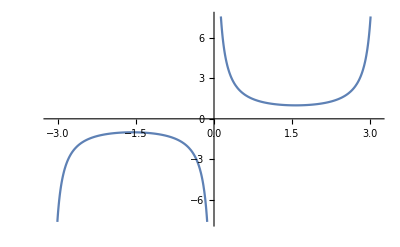

```mathematica
Plot[Csc[θ],{θ,-π,π}]
```

The transformation from a Stokes vector to a Jones vector is

```mathematica
(*Stokes2Jones[S_]:=
If[S[[3]]==0,{√((1+S[[1]])/2),√((1-S[[1]])/2)},{√((1+S[[1]])/2),√((1-S[[1]])/2)Exp[ⅈ ArcTan[√(S[[1]]^2+S[[2]]^2),S[[3]]]]}]*)
Stokes2Jones[S_]:=
If[ S[[3]]==0,{√((1+S[[1]])/2),√((1-S[[1]])/2)},
If[Abs[S[[3]]]==1,{√(1/2),√(1/2)Exp[ⅈ Sign[S[[3]]] π/2]},
{√((1+S[[1]])/2),√((1-S[[1]])/2)Exp[ⅈ Sign[S[[3]]]ArcTan[√(1-S[[3]]^2),S[[3]]]]}]]
Stokes2Jones[Normalize[{0,0,-1}]]
```

{1/(√2),-ⅈ/(√2)}

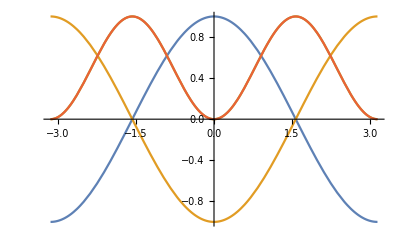

```mathematica
Plot[{Cos[θ],Cos[π-θ],Sin[θ]^2,Sin[π-θ]^2},{θ,-π,π}]
```

### Polarizabilit calcs

```mathematica
[(pow_cal_table.pow_vals)/(pi^3*const.mhe*const.c*const.epsilon0*waist_est(1)^4)]=((kg m^2)/s^3)/(kg*m/s*(s^4 A^2)/(kg m^3)*m^4)
```

Should have values in  the range of

```mathematica
physConstants = {c->299792458,m->6.64*10^-27,ϵ0->8.858*10^-12};
1/(4 π^2)1/(2 m ϵ0 c)(2 P)/(π w0^2)4/w0^2/.physConstants/.{P->110*10^-3,w0->10*10^-6}
```

2.01196×10^46

```mathematica
((kg m^2)/s^3)/(kg*m/s*(s^4 A^2)/(kg m^3)*m^4)
```

kg/(A^2 s^6)

Polz units in (C m^2)/V where C = A s, V = (kg m^2)/(s^3 A)

```mathematica
V = (kg m^2)/(A s^3);
α = (c m^2)/v/.v->V/.c-> A s
```

(A^2 s^4)/kg

the TO model is 
result = b (1) + (1/2).*x (: , 2).*cos (b (5)).*b (2) - (1/2)*D_fun (b (5), Q_fun (x (: , 1), x (: , 3), b (4))).*b (3)

```mathematica
%tune_out_scalar
%reduced_vector
%reduce_tensor
%angle between polz measurment basis and B cross k
% theta k
```

```mathematica
Dfun[θk_,Q_]:=3 Sin[θk]^2(1/2+Q/2)-1;
Qfun[Contrast_,θmin_, BasisAngle_] :=Contrast Cos[2.*(θmin+BasisAngle)];
ToFreq[fToScalar_,ReducedVector_,ReducedTensor_ ,BasisAngle_,θk_,
Contrast_,θmin_,𝒱_]:=fToScalar + 1/2 𝒱 Cos[θk] ReducedVector 1/2*Dfun [θk, Qfun [Contrast,θmin, BasisAngle]]ReducedTensor

fTO=fToScalar + 1/2 𝒱 Cos[θk] ReducedVector 1/2*Dfun [θk, Qfun [Contrast,θmin, BasisAngle]]ReducedTensor
```

fToScalar+1/4 ReducedTensor ReducedVector 𝒱 Cos[θk] (-1+3 (1/2+1/2 Contrast Cos[2. (BasisAngle+θmin)]) Sin[θk]^2)

```mathematica
D[fTO,θk]/.{ReducedTensor->βT,ReducedVector->βV}//FullSimplify
```

1/16 𝒱 βT βV (7+9 Cos[2 θk]+3 Contrast (1+3 Cos[2 θk]) Cos[2. (BasisAngle+θmin)]) Sin[θk]

```mathematica
D[fTO,BasisAngle]/.{ReducedTensor->βT,ReducedVector->βV}//FullSimplify
```

-0.75 Contrast 𝒱 βT βV Cos[θk] Sin[θk]^2 Sin[2. (BasisAngle+θmin)]